```mathematica
a = 0.963;
r0 = 2.409;
d = 0.1679;
```

```mathematica
phi[r_]:=-d Exp[-a (r-r0)] (2-Exp[-a (r-r0)])
```

```mathematica
mh = 1836;
mcl = 65092;
```

```mathematica
mr = mh mcl / (mh + mcl);
```

```mathematica
s = NDSolve[{r''[t] == -D[phi[r[t]],r[t]] / mr, r[0] == 0.8r0, r'[0] == 0}, r,{t,0,100000},MaxSteps->Infinity];
```

```mathematica
rel[t_]:= Evaluate[r[t] /. s] - r0;
```

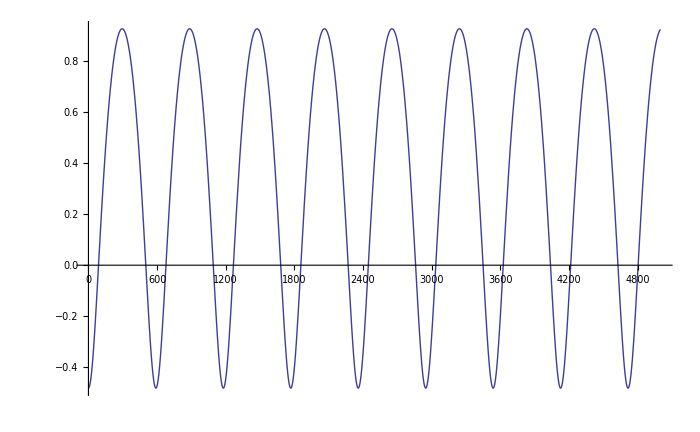

```mathematica
Plot[rel[t], {t,0,5000}, ImageSize->700]
```

```mathematica
transform = FourierTransform[rel[t],t,ω];
```

```mathematica
SetDirectory["~/lab/computazionale/dinamica.molecolare"];
```

```mathematica
list = RunThrough["./mathematica_output.py",0];
```

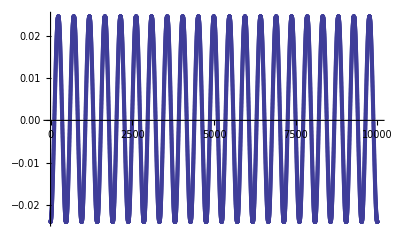

```mathematica
ListPlot[list]
```

```mathematica
Abs[Fourier[list]]^2
```

Fourier::fftl: Argument {-0.0240813`, -0.0240704`, -0.0240552`, -0.0240356`, -0.0240117`, -0.0239835`, -0.0239509`, -0.023914`, -0.0238728`, -0.0238273`, « 9990 »} is not a nonempty list or rectangular array of numeric quantities.

Abs[Fourier[{-0.0240813,-0.0240704,-0.0240552,-0.0240356,-0.0240117,-0.0239835,-0.0239509,-0.023914,-0.0238728,-0.0238273,-0.0237775,-0.0237234,-0.023665,-0.0236023,«9973»,-0.0240327,-0.0240528,-0.0240686,-0.0240801,-0.0240872,-0.02409,-0.0240884,-0.0240824,-0.0240722,-0.0240575,-0.0240386,-0.0240152,-0.0239876}]]^2

```mathematica
ListPlot[Abs[Fourier[list]]^2]
```

Fourier::fftl: Argument {-0.0240813`, -0.0240704`, -0.0240552`, -0.0240356`, -0.0240117`, -0.0239835`, -0.0239509`, -0.023914`, -0.0238728`, -0.0238273`, « 9990 »} is not a nonempty list or rectangular array of numeric quantities.

ListPlot::lpn: Abs[Fourier[{-0.0240813`, -0.0240704`, -0.0240552`, -0.0240356`, -0.0240117`, -« 10 », -0.0239509`, -0.023914`, -0.0238728`, -0.0238273`, « 9990 »}]]^2 is not a list of numbers or pairs of numbers.

ListPlot[Abs[Fourier[{-0.0240813,-0.0240704,-0.0240552,-0.0240356,-0.0240117,-0.0239835,-0.0239509,-0.023914,-0.0238728,-0.0238273,-0.0237775,-0.0237234,-0.023665,«9974»,-0.0240327,-0.0240528,-0.0240686,-0.0240801,-0.0240872,-0.02409,-0.0240884,-0.0240824,-0.0240722,-0.0240575,-0.0240386,-0.0240152,-0.0239876}]]^2]